```mathematica
CC
dp[0]=dp[1]=0;
dp[i_]:=dp[i]=With[{l=Rest@Reverse@Divisors[i]},Min[dp/@l+i/l+2]]
```

所有临时定义已清空!

```mathematica
dp[i_]:=dp[i]=Min[dp/@Divisors[i]+i/Divisors[i]+2]
```

```mathematica
arr[0]=arr[1]=0;
For[i=2,i<1000+1,++i,
arr[i]=i+2;
For[j=2,j*j≤i,++j,
If[Mod[i,j]==0,
arr[i]=Min[arr[i],arr[j]+i/j+2];
arr[i]=Min[arr[i],arr[i/j]+j+2]
]
]
]
```

```mathematica
Min[dp/@Divisors[2]+2/Divisors[2]+2]
```

$RecursionLimit::reclim2: 在 dp[1] 计算过程中超过 1024 的递归深度.

Hold[Min[dp/@Divisors[2]+2/Divisors[2]+2]]

```mathematica
Array[dp,100]
```

{0,4,5,6,7,8,9,10,10,11,13,11,15,13,12,12,19,13,21,13,14,17,25,14,14,19,15,15,31,15,33,16,18,23,16,16,39,25,20,17,43,17,45,19,17,29,49,17,18,18,24,21,55,18,20,19,26,35,61,18,63,37,19,18,22,21,69,25,30,20,73,19,75,43,19,27,22,23,81,19,20,47,85,20,26,49,36,23,91,20,24,31,38,53,28,20,99,22,23,20}

```mathematica
Array[dp,100]
```

{0,4,5,6,7,8,9,10,10,11,13,11,15,13,12,12,19,13,21,13,14,17,25,14,14,19,15,15,31,15,33,16,18,23,16,16,39,25,20,17,43,17,45,19,17,29,49,17,18,18,24,21,55,18,20,19,26,35,61,18,63,37,19,18,22,21,69,25,30,20,73,19,75,43,19,27,22,23,81,19,20,47,85,20,26,49,36,23,91,20,24,31,38,53,28,20,99,22,23,20}

```mathematica
{0,4,5,6,7,8,9,10,10,11,13,11,15,13,12,12,19,13,21,13,14,17,25,14,14,19,15,15,31,15,33,16,18,23,16,16,39,25,20,17,43,17,45,19,17,29,49,17,18,18,24,21,55,18,20,19,26,35,61,18,63,37,19,18,22,21,69,25,30,20,73,19,75,43,19,27,22,23,81,19,20,47,85,20,26,49,36,23,91,20,24,31,38,53,28,20,99,22,23,20}=={0,4,5,6,7,8,9,10,10,11,13,11,15,13,12,12,19,13,21,13,14,17,25,14,14,19,15,15,31,15,33,16,18,23,16,16,39,25,20,17,43,17,45,19,17,29,49,17,18,18,24,21,55,18,20,19,26,35,61,18,63,37,19,18,22,21,69,25,30,20,73,19,75,43,19,27,22,23,81,19,20,47,85,20,26,49,36,23,91,20,24,31,38,53,28,20,99,22,23,20}
```

True

```mathematica
dp[55]=57
dp[15]=Min[dp[55],dp[5]+55/5+2]
dp[15]=Min[dp[55],dp[11]+5+2]
```

57

20

20

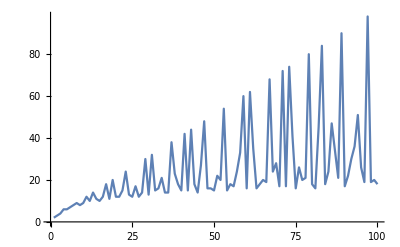

```mathematica
fa[i_]:=Total[(#1+1)#2&@@@FactorInteger[i]]
Array[fa,100]//ListLinePlot
```

```mathematica
(#1+1)#2@@@
```

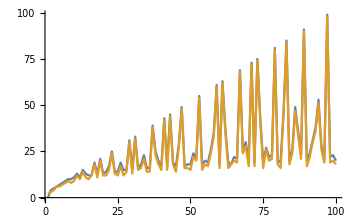

```mathematica
{Array[dp,100],Array[fa,100]}//ListLinePlot
```

```mathematica
Array[dp,100]-Array[fa,100]
```

{-2,1,1,0,1,1,1,1,2,2,1,1,1,2,2,0,1,2,1,1,2,2,1,1,2,2,3,1,1,2,1,1,2,2,2,2,1,2,2,2,1,2,1,1,3,2,1,1,2,3,2,1,1,3,2,2,2,2,1,2,1,2,3,0,2,2,1,1,2,3,1,2,1,2,3,1,2,2,1,1,4,2,1,2,2,2,2,2,1,3,2,1,2,2,2,1,1,3,3,2}

```mathematica
dp[i_]:=dp[i]=Min[dp/@Divisors[i]+i/Divisors[i]+2]
```

```mathematica
Length[{{2,2},{3,1}}]
```

2

```mathematica
3^(4-n+5 Floor[n/5]) 4^(n-3-4 Floor[n/5])/.n->100

LinearRecurrence[
{0,0,0,0,4},
{1,2,3,4,5,6,9,12,16,20,27,36,48,64,81},
{100}
]//First

nt=x (1+2 x+3 x^2+4 x^3+5 x^4+2 x^5+x^6+3 x^10+x^14);
SeriesCoefficient[Series[nt/(1-4*x^5),{x,0,100}],100]
```

1391569403904

1391569403904

1391569403904

```mathematica
nt/(1-4*x^5)//Expand
```

x/(1-4 x^5)+(2 x^2)/(1-4 x^5)+(3 x^3)/(1-4 x^5)+(4 x^4)/(1-4 x^5)+(5 x^5)/(1-4 x^5)+(2 x^6)/(1-4 x^5)+x^7/(1-4 x^5)+(3 x^11)/(1-4 x^5)+x^15/(1-4 x^5)

所有临时定义已清空!

```mathematica
CC
dp[0]=dp[1]=1;
dl[0,1]=dl[0,b_]=1
dl[a_,0]:=dp[a]
dp[i_]:=dp[i]=With[
{l=Rest@Reverse@Divisors[i]},
Min@Join[dp/@l+i/l+2,{dp[i-1]+1}]
];
dl[i_,n_]:=dl[i,n]=With[
{l=Rest@Reverse@Divisors[i]},
Min@Join[dl[#,n]&/@l+i/l+2,{dl[i-1,n]+1,dl[i+1,n-1]-1}]
];
```

所有临时定义已清空!

1

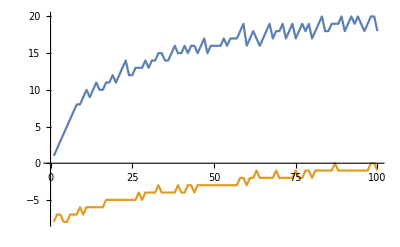

```mathematica
{Array[dp,100],Array[dl[#,20]&,100]}//ListLinePlot
```

```mathematica
CC
stdp[1]=ConstantArray["V",dp[1]=0];
dp[i_]:=dp[i]=With[{l=Rest@Reverse@Divisors[i]},Min[dp/@l+i/l+2]];
stdp[i_]:=stdp[i]=Block[
{l=Rest@Reverse@Divisors[i],st},
st=Take[l,Ordering[dp/@l+i/l+2,1]];
Join[stdp@@st,{"A","C"},ConstantArray["V",i/First@st]]
]
TableForm[StringJoin@@@Array[stdp,20],TableHeadings->{Range[20],None}]
```

所有临时定义已清空!

1 | 
2 | ACVV
3 | ACVVV
4 | ACVVVV
5 | ACVVVVV
6 | ACVVVVVV
7 | ACVVVVVVV
8 | ACVVVVACVV
9 | ACVVVACVVV
10 | ACVVVVVACVV
11 | ACVVVVVVVVVVV
12 | ACVVVVACVVV
13 | ACVVVVVVVVVVVVV
14 | ACVVVVVVVACVV
15 | ACVVVVVACVVV
16 | ACVVVVACVVVV
17 | ACVVVVVVVVVVVVVVVVV
18 | ACVVVVVVACVVV
19 | ACVVVVVVVVVVVVVVVVVVV
20 | ACVVVVVACVVVV

```mathematica
StringLength/@StringJoin@@@Array[stdp,20]
Array[dp,20]
```

{0,4,5,6,7,8,9,10,10,11,13,11,15,13,12,12,19,13,21,13}

{0,4,5,6,7,8,9,10,10,11,13,11,15,13,12,12,19,13,21,13}

```mathematica
CC
stdp[1]=ConstantArray["P",dp[1]=1];
dp[i_]:=dp[i]=With[
{l=Rest@Reverse@Divisors[i]},
Min@Append[dp/@l+i/l+2,dp[i-1]+1]
];
stdp[i_]:=stdp[i]=Block[
{l=Rest@Reverse@Divisors[i],st},
st=Ordering[Join[dp/@l+i/l+2,{dp[i-1]+1}],1];
If[First@st>Length[l],
Append[stdp[i-1],"P"],
Join[stdp@@Take[l,st],{"A","C"},ConstantArray["V",i/First@Take[l,st]]]
]
]
TableForm[StringJoin@@@Array[stdp,20],TableHeadings->{Range[20],None}]
```

所有临时定义已清空!

1 | P
2 | PP
3 | PPP
4 | PPPP
5 | PPPPP
6 | PPPPPP
7 | PPPPPPP
8 | PPPPACVV
9 | PPPACVVV
10 | PPPPPACVV
11 | PPPPPACVVP
12 | PPPPACVVV
13 | PPPPACVVVP
14 | PPPPPPPACVV
15 | PPPPPACVVV
16 | PPPPACVVVV
17 | PPPPACVVVVP
18 | PPPPPPACVVV
19 | PPPPPPACVVVP
20 | PPPPPACVVVV